This shows how to call the connecting routine with Mathematica

First compile the source using 

cd Ultraspherical
mcc ultrasolve.tm UltrasphericalMathLink.cpp AdaptiveQR.cpp FilledBandedOperator.cpp UltrasphericalOperator.cpp Operator.cpp -o UltrasphericalMathLink


We can now install the compiled file:

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];
```

This installs UltrasphericalSolve[{a0,...,an}], which solves the ODE u’’ + (a0 T0(x) + ... + an Tn(x)) u = 0, u(-1) = 1, u(1) = 0.

```mathematica
a=Exp[#]&//Fun;b=AiryAi[#]&//Fun;f=Cos[Cos[#]]&//Fun;
```

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];U=PoissonSolve[a//DCT,b//DCT,{3,1},{10}];
```

```mathematica
Length/@U
```

{487,485,481,475,467,457,445,431,415,397,377,355,331,305,277,247,215,181,145,107,67,25}

```mathematica
PadRight[U,{50,50}]
```

{{-0.241005,-0.370775,-0.0284173,-0.00354618,-0.000824185,-0.000263595,-0.000101898,-0.0000448134,-0.0000215838,-0.000011072,-5.91504×10^-6,-3.22979×10^-6,-1.77475×10^-6,-9.69345×10^-7,-5.21352×10^-7,-2.74277×10^-7,-1.40507×10^-7,-6.98927×10^-8,-3.37045×10^-8,-1.57443×10^-8,-7.12251×10^-9,-3.12066×10^-9,-1.32458×10^-9,-5.44843×10^-10,-2.17264×10^-10,-8.40196×10^-11,-3.15198×10^-11,-1.1474×10^-11,-4.05381×10^-12,-1.39028×10^-12,-4.62889×10^-13,-1.49627×10^-13,-4.69571×10^-14,-1.4306×10^-14,-4.23048×10^-15,-1.21397×10^-15,-3.3791×10^-16,-9.11889×10^-17,-2.38427×10^-17,-6.0367×10^-18,-1.48014×10^-18,-3.52191×10^-19,-8.19411×10^-20,-1.90182×10^-20,-4.5962×10^-21,-1.23572×10^-21,-3.8936×10^-22,-1.41767×10^-22,-5.59235×10^-23,-2.2533×10^-23},{-0.0572669,-0.150691,-0.0487509,-0.0117468,-0.00314585,-0.00103512,-0.000403893,-0.000178339,-0.0000860642,-0.0000441958,-0.000023625,-0.0000129045,-7.09247×10^-6,-3.8743×10^-6,-2.08391×10^-6,-1.09637×10^-6,-5.6167×10^-7,-2.79397×10^-7,-1.34736×10^-7,-6.29398×10^-8,-2.84733×10^-8,-1.24754×10^-8,-5.29526×10^-9,-2.17813×10^-9,-8.68569×10^-10,-3.35891×10^-10,-1.2601×10^-10,-4.58708×10^-11,-1.62064×10^-11,-5.55812×10^-12,-1.85057×10^-12,-5.98191×10^-13,-1.87729×10^-13,-5.71937×10^-14,-1.69131×10^-14,-4.85334×10^-15,-1.35093×10^-15,-3.64565×10^-16,-9.53208×10^-17,-2.41341×10^-17,-5.91744×10^-18,-1.40802×10^-18,-3.27593×10^-19,-7.60347×10^-20,-1.83764×10^-20,-4.94105×10^-21,-1.55702×10^-21,-5.66959×10^-22,-2.23661×10^-22,-9.01199×10^-23},{-0.012293,-0.0415309,-0.032301,-0.0145879,-0.00548775,-0.0020821,-0.000859335,-0.00038887,-0.000189949,-0.000098178,-0.0000526749,-0.0000288344,-0.0000158682,-8.67485×10^-6,-4.66826×10^-6,-2.45675×10^-6,-1.25882×10^-6,-6.26264×10^-7,-3.02033×10^-7,-1.41099×10^-7,-6.38348×10^-8,-2.79701×10^-8,-1.18725×10^-8,-4.88379×10^-9,-1.94756×10^-9,-7.53183×10^-10,-2.82566×10^-10,-1.02864×10^-10,-3.63436×10^-11,-1.24646×10^-11,-4.15017×10^-12,-1.34156×10^-12,-4.21026×10^-13,-1.28272×10^-13,-3.79324×10^-14,-1.08851×10^-14,-3.0299×10^-15,-8.17651×10^-16,-2.13785×10^-16,-5.41275×10^-17,-1.32713×10^-17,-3.15783×10^-18,-7.34729×10^-19,-1.70552×10^-19,-4.12324×10^-20,-1.10924×10^-20,-3.49761×10^-21,-1.27418×10^-21,-5.02775×10^-22,-2.02602×10^-22},{-0.00281676,-0.0104226,-0.0140626,-0.010589,-0.00581999,-0.00279348,-0.00130887,-0.000631998,-0.000319355,-0.00016816,-0.0000911869,-0.00005023,-0.0000277467,-0.0000152032,-8.19279×10^-6,-4.3153×10^-6,-2.21231×10^-6,-1.10101×10^-6,-5.31125×10^-7,-2.48167×10^-7,-1.1229×10^-7,-4.92079×10^-8,-2.08899×10^-8,-8.59403×10^-9,-3.42749×10^-9,-1.32565×10^-9,-4.97379×10^-10,-1.8108×10^-10,-6.39836×10^-11,-2.19458×10^-11,-7.30748×10^-12,-2.36231×10^-12,-7.4141×10^-13,-2.25891×10^-13,-6.68025×10^-14,-1.91701×10^-14,-5.33611×10^-15,-1.44×10^-15,-3.76501×10^-16,-9.53219×10^-17,-2.33709×10^-17,-5.56089×10^-18,-1.29397×10^-18,-3.00475×10^-19,-7.27071×10^-20,-1.95904×10^-20,-6.18839×10^-21,-2.25753×10^-21,-8.91427×10^-22,-3.59311×10^-22},{-0.000766464,-0.00295704,-0.005304,-0.00575053,-0.00441295,-0.00274248,-0.00153159,-0.000824289,-0.000444001,-0.000242686,-0.000134534,-0.0000750943,-0.0000418152,-0.0000230238,-0.0000124444,-6.5668×10^-6,-3.37052×10^-6,-1.67871×10^-6,-8.10235×10^-7,-3.78732×10^-7,-1.71424×10^-7,-7.51428×10^-8,-3.19081×10^-8,-1.31301×10^-8,-5.23777×10^-9,-2.02625×10^-9,-7.60399×10^-10,-2.7689×10^-10,-9.7855×10^-11,-3.35689×10^-11,-1.11794×10^-11,-3.61445×10^-12,-1.13452×10^-12,-3.45697×10^-13,-1.0224×10^-13,-2.93409×10^-14,-8.1674×10^-15,-2.20404×10^-15,-5.76244×10^-16,-1.45882×10^-16,-3.57644×10^-17,-8.50965×10^-18,-1.98052×10^-18,-4.6027×10^-19,-1.11594×10^-19,-3.01724×10^-20,-9.56928×10^-21,-3.50136×10^-21,-1.38472×10^-21,-5.58465×10^-22},{-0.00025545,-0.00100454,-0.00203504,-0.00275749,-0.00272888,-0.00214192,-0.00144245,-0.000888923,-0.000524392,-0.000303822,-0.000174686,-0.0000997402,-0.0000563227,-0.0000312814,-0.0000169983,-8.99985×10^-6,-4.62913×10^-6,-2.30881×10^-6,-1.11545×10^-6,-5.2179×10^-7,-2.36321×10^-7,-1.03645×10^-7,-4.40327×10^-8,-1.81276×10^-8,-7.23453×10^-9,-2.79986×10^-9,-1.05112×10^-9,-3.82893×10^-10,-1.35363×10^-10,-4.64502×10^-11,-1.54735×10^-11,-5.00404×10^-12,-1.57103×10^-12,-4.78787×10^-13,-1.41621×10^-13,-4.06463×10^-14,-1.13149×10^-14,-3.05338×10^-15,-7.98243×10^-16,-2.02057×10^-16,-4.95289×10^-17,-1.17843×10^-17,-2.74373×10^-18,-6.38629×10^-19,-1.55428×10^-19,-4.2301×10^-20,-1.3517×10^-20,-4.97342×10^-21,-1.97252×10^-21,-7.96355×10^-22},{-0.00010022,-0.000397361,-0.000846947,-0.00129475,-0.00152145,-0.00143796,-0.00114874,-0.000814586,-0.00053417,-0.00033349,-0.000201639,-0.000118975,-0.0000686125,-0.000038617,-0.0000211607,-0.0000112631,-5.81307×10^-6,-2.90595×10^-6,-1.40624×10^-6,-6.58646×10^-7,-2.98615×10^-7,-1.31087×10^-7,-5.57385×10^-8,-2.29651×10^-8,-9.17202×10^-9,-3.55224×10^-9,-1.33449×10^-9,-4.86421×10^-10,-1.72064×10^-10,-5.90758×10^-11,-1.96888×10^-11,-6.36996×10^-12,-2.00059×10^-12,-6.09888×10^-13,-1.80442×10^-13,-5.17965×10^-14,-1.44199×10^-14,-3.89116×10^-15,-1.01712×10^-15,-2.57402×10^-16,-6.30787×10^-17,-1.50072×10^-17,-3.49668×10^-18,-8.16148×10^-19,-1.99976×10^-19,-5.50517×10^-20,-1.7818×10^-20,-6.61726×10^-21,-2.63685×10^-21,-1.06636×10^-21},{-0.0000442442,-0.000176088,-0.000384143,-0.000625049,-0.00081661,-0.000882232,-0.000810268,-0.000652928,-0.000476235,-0.000322746,-0.000207114,-0.000127349,-0.0000754948,-0.0000432638,-0.000023985,-0.0000128631,-6.6721×10^-6,-3.34688×10^-6,-1.62371×10^-6,-7.62021×10^-7,-3.46067×10^-7,-1.52148×10^-7,-6.47844×10^-8,-2.67275×10^-8,-1.06881×10^-8,-4.14436×10^-9,-1.55868×10^-9,-5.68736×10^-10,-2.01376×10^-10,-6.92009×10^-11,-2.30816×10^-11,-7.47289×10^-12,-2.3484×10^-12,-7.16276×10^-13,-2.11999×10^-13,-6.08707×10^-14,-1.69479×10^-14,-4.57307×10^-15,-1.19508×10^-15,-3.02315×10^-16,-7.40525×10^-17,-1.76167×10^-17,-4.11003×10^-18,-9.63973×10^-19,-2.3894×10^-19,-6.70426×10^-20,-2.21498×10^-20,-8.34585×10^-21,-3.34944×10^-21,-1.35794×10^-21},{-0.0000211174,-0.0000842049,-0.000185852,-0.000312489,-0.000434468,-0.000513095,-0.000522912,-0.000468091,-0.000375587,-0.000275588,-0.00018812,-0.000121041,-0.0000740844,-0.0000433916,-0.0000244112,-0.0000132216,-6.90487×10^-6,-3.48066×10^-6,-1.69497×10^-6,-7.97923×10^-7,-3.6335×10^-7,-1.6014×10^-7,-6.83447×10^-8,-2.82581×10^-8,-1.13237×10^-8,-4.39945×10^-9,-1.65769×10^-9,-6.05906×10^-10,-2.14878×10^-10,-7.39477×10^-11,-2.46969×10^-11,-8.00498×10^-12,-2.51807×10^-12,-7.68642×10^-13,-2.27637×10^-13,-6.53865×10^-14,-1.82079×10^-14,-4.91238×10^-15,-1.28319×10^-15,-3.24374×10^-16,-7.93972×10^-17,-1.88868×10^-17,-4.41695×10^-18,-1.04492×10^-18,-2.64187×10^-19,-7.64746×10^-20,-2.60827×10^-20,-1.00392×10^-20,-4.06992×10^-21,-1.65566×10^-21},{-0.0000103582,-0.0000413448,-0.0000918201,-0.000157148,-0.000226425,-0.000282727,-0.000309478,-0.000299699,-0.00025971,-0.000204107,-0.000147479,-0.0000991963,-0.0000627546,-0.0000376439,-0.0000215411,-0.0000118104,-6.22368×10^-6,-3.15923×10^-6,-1.54727×10^-6,-7.32013×10^-7,-3.34839×10^-7,-1.48195×10^-7,-6.34989×10^-8,-2.63541×10^-8,-1.05988×10^-8,-4.13185×10^-9,-1.56182×10^-9,-5.72557×10^-10,-2.03603×10^-10,-7.02398×10^-11,-2.351×10^-11,-7.63492×10^-12,-2.40559×10^-12,-7.35281×10^-13,-2.17973×10^-13,-6.26487×10^-14,-1.74485×10^-14,-4.70598×10^-15,-1.22822×10^-15,-3.10073×10^-16,-7.57974×10^-17,-1.80312×10^-17,-4.23715×10^-18,-1.01884×10^-18,-2.66908×10^-19,-8.13625×10^-20,-2.91214×10^-20,-1.15493×10^-20,-4.74551×10^-21,-1.93872×10^-21},{-4.63818×10^-6,-0.0000185233,-0.0000412739,-0.0000713203,-0.000104824,-0.000135257,-0.000154892,-0.000158235,-0.000145046,-0.000120284,-0.000091162,-0.000063827,-0.00004171,-0.0000256704,-0.0000149898,-8.35291×10^-6,-4.46111×10^-6,-2.29077×10^-6,-1.13354×10^-6,-5.41388×10^-7,-2.49861×10^-7,-1.11526×10^-7,-4.81743×10^-8,-2.01479×10^-8,-8.16189×10^-9,-3.20356×10^-9,-1.21861×10^-9,-4.49344×10^-10,-1.60636×10^-10,-5.56812×10^-11,-1.87158×10^-11,-6.10021×10^-12,-1.92795×10^-12,-5.90735×10^-13,-1.75433×10^-13,-5.04732×10^-14,-1.40593×10^-14,-3.78853×10^-15,-9.8684×10^-16,-2.48436×10^-16,-6.05691×10^-17,-1.44171×10^-17,-3.42653×10^-18,-8.53792×10^-19,-2.40003×10^-19,-8.0021×10^-20,-3.07966×10^-20,-1.2716×10^-20,-5.3131×10^-21,-2.18096×10^-21},{-9.43105×10^-7,-3.76795×10^-6,-8.41658×10^-6,-0.0000146485,-0.0000218605,-0.0000289614,-0.0000344861,-0.0000370632,-0.0000360471,-0.0000318578,-0.0000257456,-0.000019176,-0.000013277,-8.61709×10^-6,-5.28195×10^-6,-3.07704×10^-6,-1.71214×10^-6,-9.13353×10^-7,-4.68387×10^-7,-2.31344×10^-7,-1.10195×10^-7,-5.06648×10^-8,-2.24988×10^-8,-9.65441×10^-9,-4.00463×10^-9,-1.60621×10^-9,-6.23105×10^-10,-2.33854×10^-10,-8.49265×10^-11,-2.98491×10^-11,-1.01545×10^-11,-3.34386×10^-12,-1.06577×10^-12,-3.28706×10^-13,-9.80595×10^-14,-2.82753×10^-14,-7.87283×10^-15,-2.11421×10^-15,-5.47074×10^-16,-1.3648×10^-16,-3.30098×10^-17,-7.8882×10^-18,-1.95193×10^-18,-5.42643×10^-19,-1.81647×10^-19,-7.17937×10^-20,-3.08066×10^-20,-1.33929×10^-20,-5.70406×10^-21,-2.35189×10^-21},{-2.6889×10^-9,-1.0743×10^-8,-2.39992×10^-8,-4.17811×10^-8,-6.23948×10^-8,-8.2788×10^-8,-9.88879×10^-8,-1.06908×10^-7,-1.05052×10^-7,-9.43723×10^-8,-7.81076×10^-8,-6.00896×10^-8,-4.33536×10^-8,-2.9571×10^-8,-1.91973×10^-8,-1.1924×10^-8,-7.11376×10^-9,-4.0875×10^-9,-2.26615×10^-9,-1.21359×10^-9,-6.28141×10^-10,-3.14271×10^-10,-1.51955×10^-10,-7.09648×10^-11,-3.19797×10^-11,-1.38865×10^-11,-5.79845×10^-12,-2.32127×10^-12,-8.86935×10^-13,-3.21204×10^-13,-1.08985×10^-13,-3.392×10^-14,-9.25542×10^-15,-1.94342×10^-15,-1.19383×10^-16,1.75713×10^-16,1.36947×10^-16,7.06004×10^-17,2.99755×10^-17,1.09209×10^-17,3.32641×10^-18,7.23288×10^-19,-3.18882×10^-21,-1.26884×10^-19,-1.00163×10^-19,-5.80154×10^-20,-2.92019×10^-20,-1.3483×10^-20,-5.85172×10^-21,-2.41873×10^-21},{-3.63186×10^-12,-1.44275×10^-11,-3.10933×10^-11,-4.8295×10^-11,-5.29368×10^-11,-2.26824×10^-11,6.80572×10^-11,2.32199×10^-10,4.52362×10^-10,6.78563×10^-10,8.4919×10^-10,9.21526×10^-10,8.89285×10^-10,7.77939×10^-10,6.26639×10^-10,4.70865×10^-10,3.3361×10^-10,2.24819×10^-10,1.45106×10^-10,9.0184×10^-11,5.41897×10^-11,3.1574×10^-11,1.78762×10^-11,9.84847×10^-12,5.28449×10^-12,2.76315×10^-12,1.40823×10^-12,6.99529×10^-13,3.38618×10^-13,1.59664×10^-13,7.32851×10^-14,3.27146×10^-14,1.41849×10^-14,5.96329×10^-15,2.42438×10^-15,9.49566×10^-16,3.5623×10^-16,1.26794×10^-16,4.21×10^-17,1.25974×10^-17,3.10507×10^-18,4.13766×10^-19,-1.70033×10^-19,-1.96833×10^-19,-1.25493×10^-19,-6.61239×10^-20,-3.14542×10^-20,-1.39777×10^-20,-5.90065×10^-21,-2.38837×10^-21},{1.37848×10^-14,7.12105×10^-14,3.80526×10^-13,1.80334×10^-12,6.47922×10^-12,1.81634×10^-11,4.14541×10^-11,7.92857×10^-11,1.29516×10^-10,1.83303×10^-10,2.27662×10^-10,2.51261×10^-10,2.49514×10^-10,2.25688×10^-10,1.88113×10^-10,1.46044×10^-10,1.06628×10^-10,7.38218×10^-11,4.88036×10^-11,3.0982×10^-11,1.89693×10^-11,1.12379×10^-11,6.45661×10^-12,3.6029×10^-12,1.95434×10^-12,1.03086×10^-12,5.28707×10^-13,2.63541×10^-13,1.27568×10^-13,5.98879×10^-14,2.72174×10^-14,1.19429×10^-14,5.03992×10^-15,2.03309×10^-15,7.76232×10^-16,2.75524×10^-16,8.76039×10^-17,2.25815×10^-17,2.80389×10^-18,-1.77514×10^-18,-1.97845×10^-18,-1.31718×10^-18,-7.3343×10^-19,-3.70045×10^-19,-1.74682×10^-19,-7.8401×10^-20,-3.37643×10^-20,-1.40314×10^-20,-5.64688×10^-21,-2.20573×10^-21},{1.14369×10^-17,6.52475×10^-18,-5.32535×10^-16,-4.02196×10^-15,-1.87751×10^-14,-7.01955×10^-14,-2.24544×10^-13,-6.16971×10^-13,-1.44272×10^-12,-2.85977×10^-12,-4.82558×10^-12,-7.00331×10^-12,-8.86176×10^-12,-9.92442×10^-12,-9.98565×10^-12,-9.15654×10^-12,-7.7528×10^-12,-6.13244×10^-12,-4.57796×10^-12,-3.25328×10^-12,-2.21658×10^-12,-1.45633×10^-12,-9.26869×10^-13,-5.73412×10^-13,-3.4573×10^-13,-2.03546×10^-13,-1.17178×10^-13,-6.60268×10^-14,-3.64417×10^-14,-1.9711×10^-14,-1.04526×10^-14,-5.43594×10^-15,-2.77316×10^-15,-1.38809×10^-15,-6.81856×10^-16,-3.28758×10^-16,-1.55612×10^-16,-7.2321×10^-17,-3.30066×10^-17,-1.47948×10^-17,-6.5138×10^-18,-2.81714×10^-18,-1.19687×10^-18,-4.99504×10^-19,-2.04762×10^-19,-8.24334×10^-20,-3.25816×10^-20,-1.26377×10^-20,-4.80735×10^-21,-1.79181×10^-21},{3.0011×10^-20,9.64525×10^-20,-3.85491×10^-19,-1.18477×10^-17,-1.28549×10^-16,-8.44556×10^-16,-3.89588×10^-15,-1.36459×10^-14,-3.7987×10^-14,-8.65461×10^-14,-1.64909×10^-13,-2.67654×10^-13,-3.763×10^-13,-4.65614×10^-13,-5.14732×10^-13,-5.15598×10^-13,-4.74076×10^-13,-4.04852×10^-13,-3.24488×10^-13,-2.46332×10^-13,-1.78506×10^-13,-1.24286×10^-13,-8.35869×10^-14,-5.45303×10^-14,-3.46214×10^-14,-2.14453×10^-14,-1.29836×10^-14,-7.69316×10^-15,-4.4654×10^-15,-2.54062×10^-15,-1.41751×10^-15,-7.75778×10^-16,-4.16535×10^-16,-2.19438×10^-16,-1.13432×10^-16,-5.75337×10^-17,-2.86327×10^-17,-1.39806×10^-17,-6.69685×10^-18,-3.14654×10^-18,-1.44988×10^-18,-6.5502×10^-19,-2.9004×10^-19,-1.2582×10^-19,-5.34421×10^-20,-2.22087×10^-20,-9.02028×10^-21,-3.57574×10^-21,-1.38074×10^-21,-5.17912×10^-22},{5.78255×10^-24,-1.55369×10^-23,-3.89415×10^-22,2.57474×10^-21,6.08664×10^-20,4.69658×10^-19,2.27907×10^-18,8.08886×10^-18,2.24385×10^-17,5.05884×10^-17,9.55004×10^-17,1.55163×10^-16,2.22908×10^-16,2.90425×10^-16,3.50476×10^-16,3.97418×10^-16,4.26638×10^-16,4.34771×10^-16,4.20892×10^-16,3.87421×10^-16,3.39746×10^-16,2.84709×10^-16,2.28843×10^-16,1.77125×10^-16,1.32527×10^-16,9.61914×10^-17,6.79361×10^-17,4.68066×10^-17,3.15248×10^-17,2.07894×10^-17,1.34406×10^-17,8.52695×10^-18,5.31219×10^-18,3.2515×10^-18,1.9561×10^-18,1.15698×10^-18,6.72943×10^-19,3.84971×10^-19,2.16639×10^-19,1.19937×10^-19,6.53321×10^-20,3.5018×10^-20,1.84706×10^-20,9.58787×10^-21,4.89821×10^-21,2.46297×10^-21,1.21911×10^-21,5.94073×10^-22,2.85027×10^-22,1.34651×10^-22},{2.04247×10^-26,2.13597×10^-26,-5.8661×10^-25,7.33745×10^-24,4.4539×10^-22,8.0917×10^-21,8.21409×10^-20,5.53496×10^-19,2.70549×10^-18,1.01132×10^-17,2.99529×10^-17,7.22199×10^-17,1.45038×10^-16,2.47629×10^-16,3.66211×10^-16,4.77206×10^-16,5.56565×10^-16,5.89293×10^-16,5.73742×10^-16,5.19577×10^-16,4.42122×10^-16,3.56659×10^-16,2.74862×10^-16,2.03682×10^-16,1.45923×10^-16,1.01522×10^-16,6.88346×10^-17,4.56118×10^-17,2.9601×10^-17,1.88451×10^-17,1.17836×10^-17,7.24306×10^-18,4.37932×10^-18,2.60569×10^-18,1.52619×10^-18,8.80158×10^-19,4.99855×10^-19,2.79582×10^-19,1.54024×10^-19,8.35821×10^-20,4.46785×10^-20,2.35265×10^-20,1.22036×10^-20,6.23571×10^-21,3.13864×10^-21,1.55621×10^-21,7.60203×10^-22,3.65925×10^-22,1.73559×10^-22,8.11135×10^-23},{-2.62277×10^-30,1.12664×10^-29,3.9749×10^-28,-6.46081×10^-27,-6.72957×10^-25,-1.38493×10^-23,-1.47393×10^-22,-1.01913×10^-21,-5.08621×10^-21,-1.94343×10^-20,-5.90528×10^-20,-1.46739×10^-19,-3.0508×10^-19,-5.41398×10^-19,-8.34929×10^-19,-1.13732×10^-18,-1.38881×10^-18,-1.54081×10^-18,-1.57204×10^-18,-1.4911×10^-18,-1.32767×10^-18,-1.1193×10^-18,-9.00192×10^-19,-6.95139×10^-19,-5.18265×10^-19,-3.74781×10^-19,-2.63869×10^-19,-1.81427×10^-19,-1.22111×10^-19,-8.06008×10^-20,-5.22463×10^-20,-3.32918×10^-20,-2.08686×10^-20,-1.28747×10^-20,-7.81988×10^-21,-4.67712×10^-21,-2.75508×10^-21,-1.59862×10^-21,-9.14026×10^-22,-5.15363×10^-22,-2.87045×10^-22,-1.58461×10^-22,-8.71838×10^-23,-4.81278×10^-23,-2.67335×10^-23,-1.48088×10^-23,-8.00505×10^-24,-4.16484×10^-24,-2.12383×10^-24,-1.06605×10^-24},{-4.1628×10^-33,-3.22887×10^-32,-1.46746×10^-31,3.2768×10^-31,-1.17428×10^-28,-1.02277×10^-27,3.3114×10^-26,7.98992×10^-25,8.64483×10^-24,5.9903×10^-23,2.97816×10^-22,1.12666×10^-21,3.37226×10^-21,8.22943×10^-21,1.67888×10^-20,2.9262×10^-20,4.44158×10^-20,5.97183×10^-20,7.22105×10^-20,7.95969×10^-20,8.09541×10^-20,7.67884×10^-20,6.85798×10^-20,5.81526×10^-20,4.71599×10^-20,3.68065×10^-20,2.77925×10^-20,2.03944×10^-20,1.45968×10^-20,1.022×10^-20,7.01627×10^-21,4.73171×10^-21,3.13901×10^-21,2.05059×10^-21,1.32004×10^-21,8.37725×10^-22,5.24128×10^-22,3.23119×10^-22,1.95962×10^-22,1.16476×10^-22,6.73169×10^-23,3.72382×10^-23,1.91295×10^-23,8.61769×10^-24,3.03523×10^-24,6.26179×10^-25,-4.12278×10^-90,3.08444×10^-90,-1.45628×10^-90,4.05281×10^-91},{3.85168×10^-36,1.45053×10^-35,2.10832×10^-35,1.42223×10^-75,6.82074×10^-77,-4.65897×10^-78,1.94601×10^-79,-4.75359×10^-81,-9.49848×10^-85,6.76566×10^-84,-4.08883×10^-85,1.6343×10^-86,-5.12977×10^-88,1.33282×10^-89,-2.92639×10^-91,5.46419×10^-93,-8.64446×10^-95,1.14316×10^-96,-1.23309×10^-98,1.04478×10^-100,-6.58324×10^-103,2.8483×10^-105,-7.47463×10^-108,9.52337×10^-111,-3.42645×10^-114,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

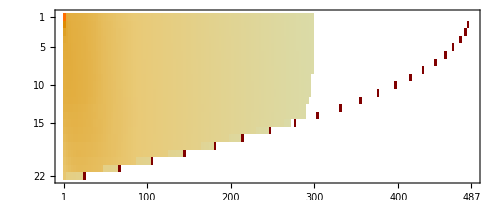

```mathematica
U//Abs//MatrixPlot
```

```mathematica
"3"
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},{10}]
```

{-0.247874,-0.594583,2.30122,-0.419138,-0.0549055,0.0139635,0.00157663,-0.0002374,-0.000019297,-5.1177×10^-6,-4.89701×10^-7,2.82999×10^-7,4.26803×10^-8,-1.91736×10^-9,-9.51222×10^-10,-1.61885×10^-10,-1.14567×10^-11,3.43466×10^-12,9.12297×10^-13,7.22144×10^-14,-6.22647×10^-15,-3.03866×10^-15,-4.84882×10^-16,-1.79416×10^-17,8.10583×10^-18,1.95887×10^-18,2.08444×10^-19,-3.09281×10^-21,-3.06823×10^-19,-6.54872×10^-20,-8.98754×10^-21,-9.42825×10^-22,-8.00475×10^-23,-6.26197×10^-24,-3.77888×10^-25,-1.38445×10^-26,-1.87504×10^-27,-7.52495×10^-29,1.03076×10^-29,-8.0746×10^-31,-2.25679×10^-32,1.04336×10^-32,-7.76054×10^-34,-7.59212×10^-35,1.08032×10^-36}

```mathematica
?ToCSeries
```

Information::notfound: Symbol "ToCSeries" not found.

```mathematica
<<Ultraspherical`
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},ConversionMatrix[2,f//Length].(f//DCT)]
```

{1.77843,-1.0268,0.233404,0.0275852,-0.0122066,-0.000798944,0.000370531,0.000015407,-2.01162×10^-6,-3.11702×10^-7,-2.02547×10^-7,-1.10707×10^-8,6.32145×10^-9,8.88606×10^-10,8.24681×10^-12,-1.44745×10^-11,-4.24162×10^-12,-4.27638×10^-13,4.81526×10^-14,1.80552×10^-14,2.24544×10^-15,3.40248×10^-17,-5.18279×10^-17,-1.13558×10^-17,-9.29563×10^-19,7.75477×10^-20,3.64148×10^-20,5.63303×10^-21,1.64602×10^-20,-3.68893×10^-21,-1.13701×10^-21,-1.81274×10^-22,-2.08773×10^-23,-1.86013×10^-24,-1.55244×10^-25,-1.05182×10^-26,-3.70396×10^-28,-4.54916×10^-29,-3.02197×10^-30,2.48427×10^-31,-1.42174×10^-32,-1.31498×10^-33,2.67939×10^-34,-1.05126×10^-35,-1.96762×10^-36}

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},(f//DCT)]//InverseDCT//Fun;
```

```mathematica
n=u//Length;
```

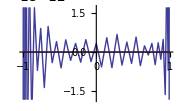

```mathematica
u''+SetLength[a,n] u'+SetLength[b,n] u-SetLength[f,n]
```

```mathematica
ConversionMatrix[1->2,n]//MatrixForm
```

(1 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | -1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | 0 | -1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/7 | 0 | -1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | -1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | -1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/10 | 0 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | -1/13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/12 | 0 | -1/14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/13 | 0 | -1/15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/14 | 0 | -1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/15 | 0 | -1/17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 0 | -1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/17 | 0 | -1/19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | -1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/19 | 0 | -1/21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | -1/22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/21 | 0 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/22 | 0 | -1/24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/23 | 0 | -1/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/24 | 0 | -1/26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/25 | 0 | -1/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/26 | 0 | -1/28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/27 | 0 | -1/29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/28 | 0 | -1/30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/29 | 0 | -1/31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/30 | 0 | -1/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/31 | 0 | -1/33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/32 | 0 | -1/34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/33 | 0 | -1/35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/34 | 0 | -1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/35 | 0 | -1/37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | -1/38 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/37 | 0 | -1/39 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/38 | 0 | -1/40 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/39 | 0 | -1/41 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/40 | 0 | -1/42 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/41 | 0 | -1/43 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/42 | 0 | -1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/43 | 0 | -1/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45)

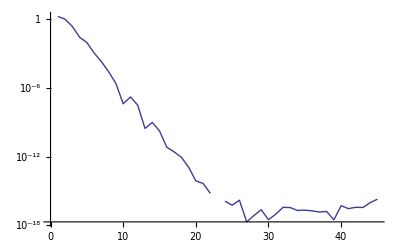

```mathematica
u//DCTPlot
```

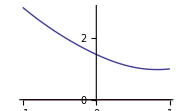

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},f//DCT]//InverseDCT//Fun
```

```mathematica
Timing[a=UltrasphericalSolve[al=Range[0,4]]]
```

{0.00018,{0.488604,-0.502508,-0.0194546,0.0167421,0.0405325,-0.0206584,-0.00982441,0.00685922,0.000293126,-0.000581009,-0.000166953,0.000169843,0.0000164067,-0.000025738,3.29936×10^-7,2.2736×10^-6,6.57296×10^-8,-3.98994×10^-7,1.00771×10^-8,4.19434×10^-8,-3.19253×10^-9,-3.41296×10^-9,3.22838×10^-10,4.41094×10^-10,-4.55209×10^-11,-3.66263×10^-11,5.19088×10^-12,2.66422×10^-12,-5.04701×10^-13,-2.78731×10^-13,4.81037×10^-14,1.93057×10^-14,-4.16034×10^-15,-1.24332×10^-15,3.59411×10^-16,1.11436×10^-16,-2.78233×10^-17,-6.57982×10^-18,2.04436×10^-18,3.71188×10^-19,-1.5747×10^-19,-2.97359×10^-20,1.05053×10^-20,1.49154×10^-21,-6.02003×10^-20,-6.4449×10^-21,4.37554×10^-21,5.22437×10^-22,-2.47318×10^-22,-3.10738×10^-23}}

We can compare the error with Mathematica:

```mathematica
<<Ultraspherical`
```

```mathematica
n=a//Length;Timing[amat=LinearSolve[Join[{DirichletOperator[-1]⟦1,;;n⟧,DirichletOperator[1]⟦1,;;n⟧},DerivativeMatrix[2,n]+ConversionMatrix[2,n].MultiplicationMatrix[al,n] //Most//Most],PadRight[{1,0},n]];]
```

{0.01878,Null}

```mathematica
amat-a//Norm
```

2.01477×10^-16